```mathematica
3
```

3

```mathematica
({r1,r2,2750.62(((rl r1)/(rl+r1))/(r2+50+(rl r1)/(rl+r1)))}/.(Solve[{r2+(r1 rl)/(r1+rl)==200,(r1(50+r2))/(r1+50+r2)==rl},{r1,r2}]//N))/.{rl->110}
```

{{-317.543,31.6987,1851.73},{317.543,118.301,898.889}}

```mathematica
310/0.112702
```

2750.62

```mathematica
2750.62(((rl r1)/(rl+r1))/(r2+50+(rl r1)/(rl+r1)))/.{r1->330,r2->100,rl->100}
```

930.979

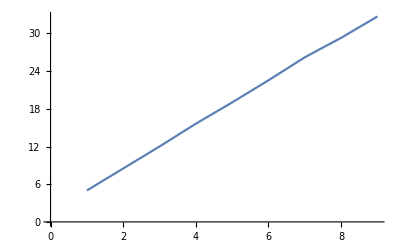

```mathematica
ListLinePlot@{{1,5.000},{2,8.500},{3,12.00},{4,15.63},{5,19.02},{6,22.54},{7,26.20},{8,29.30},{9,32.70}}
```

```mathematica
NonlinearModelFit
```

```mathematica
socket=SocketConnect["192.168.43.237:100"];
Pause[0.1];
WriteString[socket,"hellooooooooooooooooooooo"]
```

```mathematica
Close@socket
```

192.168.43.237:100

```mathematica
WriteString[socket,FromCharacterCode[1]]
```

```mathematica
Socket
```

```mathematica
2
```

2

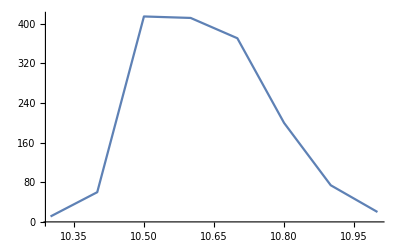

```mathematica
ListLinePlot@{{10.3,11},{10.4,60},{10.5,415},{10.6,412},{10.7,371},{10.8,200},{10.9,74},{11,20}}
```

```mathematica
ker=(N@({11,60,415,412,371,200,74,20}/1000.0))^2
```

{0.000121,0.0036,0.172225,0.169744,0.137641,0.04,0.005476,0.0004}

```mathematica
rlp=Table[0,{i,1,200}];
rlp⟦100⟧=1;
rl=Table[0,{i,1,200}];
rl⟦100⟧=1;
rl⟦102⟧=1;
rlc=3ListConvolve[ker,rl];
rlc=rlc+Table[RandomVariate[NormalDistribution[0,0.0001]],{i,1,Length[rlc]}];
```

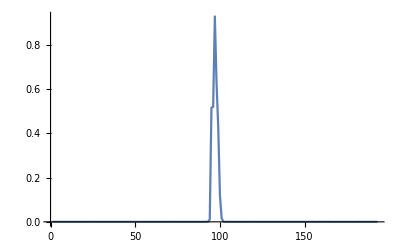

```mathematica
ListLinePlot[rlc,PlotRange->All]
```

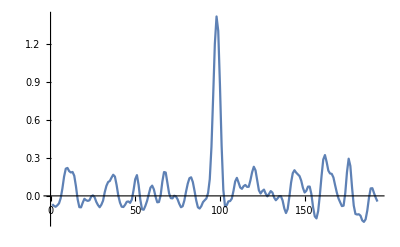

```mathematica
ListLinePlot[Chop@ListDeconvolve[ker,rlc],PlotRange->All]
```

```mathematica
kerinv=Chop@InverseFourier[If[Norm@#>100000,#/Norm[#]*100,#]&/@(1/(Fourier@ListConvolve[ker,rlp]))]⟦95;;110⟧
```

{-0.0000123062,-0.000240223,0.0240653,-0.357292,-23.2722,1167.46,-1136.11,182.668,465.433,-377.79,-12.855,205.85,-119.425,-34.6192,83.7514,-33.1862}

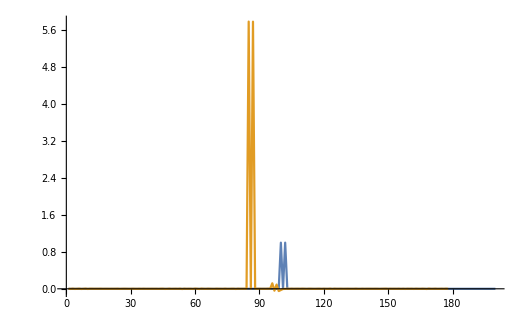

```mathematica
ListLinePlot[{rl,ListConvolve[kerinv,rlc]/100},PlotRange->All]
```

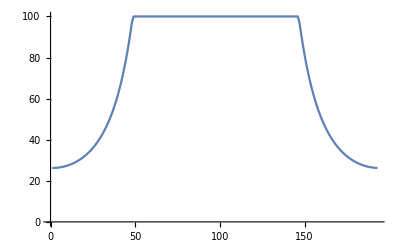

```mathematica
ListLinePlot@Abs[If[Norm@#>100,#/Norm[#]*100,#]&/@(1/(Fourier@ListConvolve[ker,rlp]))]
```

```mathematica
sigf=Piecewise[{{#-80,#≥80&&#≤100},{-80-#,#≤-80&&#≥-100}},0]&
```

Piecewise[{{#1-80, #1≥80&&#1≤100}, {-80-#1, #1≤-80&&#1≥-100}, {0, True}}]&

```mathematica
filtf=Piecewise[{{40,#≥10.5&&#≤10.9}},0]&
```

Piecewise[{{40, #1≥10.5&&#1≤10.9}, {0, True}}]&

```mathematica
Manipulate[Plot[{sigf[f],sigf[f-fc]+sigf[f+fc],filtf[f]},{f,-200,200},PlotRange->{0,100},Exclusions->None,AspectRatio->1/5,ImageSize->1000,Filling->Bottom,PlotPoints->1000],{fc,70,150}]
```

```mathematica
1.267-0.48
```

0.787

```mathematica
filtf[f]
```

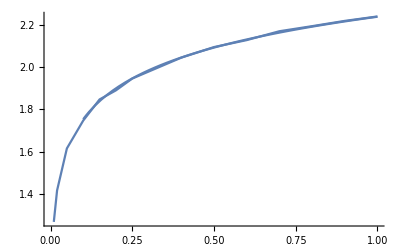

```mathematica
dat={{0.01,1.267},{0.02,1.416},{0.05,1.615},{0.1,1.747},{0.15,1.847},{0.2,1.890},{0.25,1.946},{0.3,1.979},{0.35,2.012},{0.4,2.045},{0.45,2.070},{0.5,2.095},{0.6,2.128},{0.7,2.170},{0.8,2.194},{0.9,2.219},{1.0,2.240}};
Show[ListLinePlot@dat,Plot[0.21077581192284173 Log[40996.80073378775 x],{x,0.1,1}]]
```

```mathematica
Normal@NonlinearModelFit[dat,{a Log[b x],a>0&&c>0&&b>0},{a,b,c},x,ConfidenceLevel->0.9999]
```

0.210776 Log[40996.8 x]

```mathematica
Solve[0.21077581192284173 Log[40996.80073378775 x]==y,x]
```

{{x→0.0000243921 ⅇ^(4.74438 y)}}

```mathematica
(0.000024392147243232184 ⅇ^(4.7443774068633076 1.1101))/(2 √2)
```

0.00167116

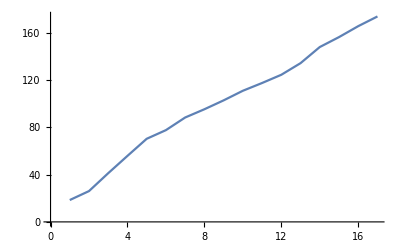

```mathematica
ListLinePlot[10^#&/@(Last/@dat)]
```

```mathematica
filtdat={{89.0,1.101},{89.1,1.424},{89.2,1.635},{89.3,1.756},{89.4,1.792},{89.5,1.785},{89.6,1.354},{89.7,1.101}};
```

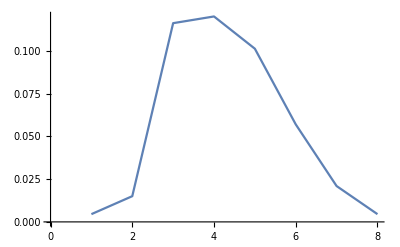

```mathematica
ListLinePlot[0.000024392147243232184 ⅇ^(4.7443774068633076 #)&/@(Reverse[Last/@filtdat])]
```

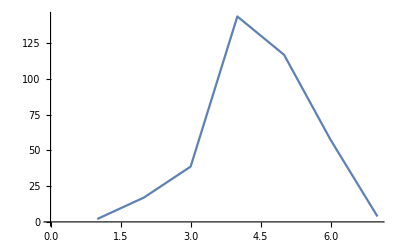

```mathematica
ListLinePlot@Reverse@{3.81,57.2,116.9,143.7,38.7,17.03,2.02}
```

```mathematica
datamp={{10.,1432.},{20.,1620.},{30.,1732.},{40.,1803.},{50.,1857.},{60.,1902.},{70.,1942.},{80.,1982.},{90.,2008.},{100.,2041.},{200.,2222.},{300.,2331.},{400.,2400.},{500.,2455.},{600.,2510.},{700.,2546.},{800.,2591.},{900.,2620.},{1000.,2640.}};
```

```mathematica
datamp=N@{{1,1159},{5,1546},{10,1735},{20,1910},{30,2015},{40,2100},{50,2159},{60,2200},{70,2240},{80,2273},{90,2300},{100,2325},{200,2512},{300,2630},{400,2700},{500,2759},{600,2803},{700,2848},{800,2885},{900,2915},{1000,2943}};
```

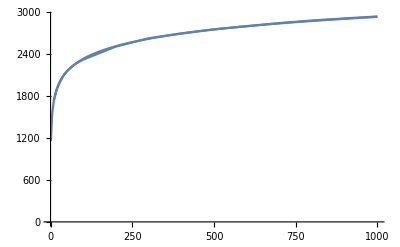

```mathematica
Show[ListLinePlot@datamp,Plot[260.77279439909387 Log[77.83900848865268 x],{x,10,1000}]]
```

```mathematica
Normal@NonlinearModelFit[datamp,{a Log[b x],a>0&&b>0},{a,b},x,ConfidenceLevel->0.9999]
```

260.773 Log[77.839 x]

```mathematica
Solve[260.77279439909387 Log[77.83900848865268 x]==y,x]
```

{{x→0.012847 ⅇ^(0.00383476 y)}}

```mathematica
mapadc=0.012847029007901344 ⅇ^(0.003834755854437685 #)&
```

0.012847 ⅇ^(0.00383476 #1)&

```mathematica
datfiltadc={{99.7,1489.},{99.8,2028.},{99.9,2040.},{100.0,1993.},{100.1,1845.},{100.2,1580.},{100.3,1190.},{100.4,1068.}};
```

```mathematica
datfiltadc={{100.4,1720.},{100.5,2500.},{100.6,2688.},{100.7,2757.},{100.8,2421.},{100.9,2205.},{101.0,1646.},{101.1,1140.}};
```

```mathematica
Last/@datfiltadc
```

{1720.,2500.,2688.,2757.,2421.,2205.,1646.,1140.}

```mathematica
convker=(mapadc/@(Last/@datfiltadc))/500;
```

```mathematica
Max@ListConvolve[deconvker,testconv]
```

99.6415

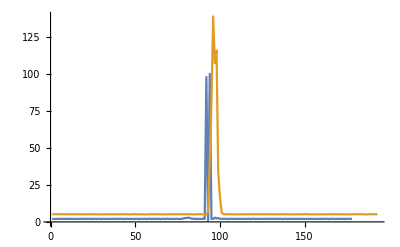

```mathematica
imp=Table[0,{i,1,200}];
imp⟦100⟧=1;
impconv=ListConvolve[convker,imp];
deconvker=(Chop@InverseFourier[1/(Fourier@impconv)]⟦88;;103⟧)/195.4;
test=Table[2,{i,1,200}];
test⟦100⟧=100;
test⟦102⟧=100;
testconv=ListConvolve[convker,test];
testconv=mapadc/@((mapdb/@testconv)+Table[RandomVariate[NormalDistribution[0,2]],{i,1,Length[testconv]}]);
ListLinePlot[{ListConvolve[deconvker,testconv],testconv},PlotRange->All]
```

```mathematica
deconvker
```

{0.0148189,-0.0112552,-0.0139333,0.053656,-0.0694247,0.00448376,0.157711,-0.312902,0.221711,0.32478,-1.15388,1.44223,-0.167504,-0.1426,0.0349846,0.0106429}

```mathematica
262.0396651971425 Log[24.00492197148314 2]
```

1014.46

```mathematica
datsmp={1258.100000,1256.600000,1240.600000,1230.800000,1238.100000,1245.600000,1249.200000,1238.200000,1237.100000,1241.500000,1238.900000,1234.800000,1236.300000,1226.300000,1232.800000,1231.900000,1228.700000,1288.100000,1227.100000,1222.900000,1240.100000,1221.600000,1389.800000,1220.600000,1219.200000,1362.100000,1267.500000,1216.200000,1241.600000,1226.300000,1231.200000,1243.300000,1436.700000,1225.700000,1209.900000,1284.400000,1369.700000,1217.800000,1205.000000,1205.700000,1199.100000,1464.200000,1235.000000,1192.400000,1227.100000,1194.100000,1414.600000,1246.300000,1195.900000,1185.700000,1187.100000,1448.600000,1212.000000,1185.100000,1183.100000,1181.000000,1303.200000,1186.200000,1172.900000,1177.100000,1176.000000,1188.000000,1173.200000,1172.200000,1166.000000,1165.700000,1167.200000,1161.300000,1178.200000,1264.600000,1332.500000,1168.600000,1162.400000,1165.700000,1162.700000,1158.300000,1156.800000,1161.700000,1329.600000,1510.300000,1598.800000,1254.800000,1161.900000,1153.000000,1148.400000,1140.700000,1141.900000,1571.100000,2355.800000,2544.600000,2622.700000,2282.800000,2071.100000,1492.900000,1142.100000,1134.000000,1137.500000,1708.700000,2497.500000,2681.100000,2755.400000,2414.900000,2210.000000,1645.800000,1131.400000,1120.800000,1120.500000,1565.500000,2355.200000,2544.700000,2623.900000,2282.400000,2073.000000,1496.600000,1123.700000,1122.800000,1124.300000,1118.800000,1316.700000,1498.000000,1585.400000,1246.500000,1130.200000,1117.700000,1118.100000,1119.700000,1118.000000,1118.400000,1136.200000,1244.200000,1316.500000,1120.700000,1114.300000,1112.600000,1113.700000,1117.300000,1115.500000,1106.200000,1113.200000,1125.900000,1133.800000,1111.300000,1108.100000,1104.200000,1106.900000,1111.200000,1107.400000,1114.800000,1110.100000,1114.100000,1111.500000,1116.000000,1106.900000,1113.400000,1113.100000,1116.000000,1112.700000,1111.300000,1114.000000,1108.200000,1111.600000,1117.200000,1115.600000,1118.100000,1110.100000,1117.300000,1117.400000,1112.500000,1121.000000,1118.600000,1115.600000,1117.100000,1125.200000,1125.300000,1128.600000,1125.300000,1124.500000,1129.400000,1130.800000,1129.400000,1120.700000,1135.400000,1133.500000,1132.800000,1131.300000,1140.000000,1137.600000,1138.200000,1141.000000,1141.900000,1139.000000,1141.600000,1147.000000,1141.900000,1148.100000,1152.200000,1146.500000,1146.600000,1150.700000,1152.600000};
```

```mathematica
mapadc/@datsmp
```

{1.59978,1.5906,1.49594,1.44077,1.48167,1.5249,1.5461,1.48224,1.476,1.50111,1.48622,1.46304,1.47148,1.41612,1.45186,1.44686,1.42921,1.79482,1.42047,1.39777,1.49308,1.39082,2.6509,1.3855,1.37808,2.38376,1.65849,1.36232,1.50169,1.41612,1.44298,1.51151,3.17323,1.41286,1.3298,1.76954,2.45425,1.3707,1.30505,1.30855,1.27585,3.52615,1.46416,1.24349,1.42047,1.25162,2.91539,1.529,1.26029,1.21195,1.21847,3.32139,1.34055,1.20916,1.19992,1.1903,1.90182,1.21427,1.15389,1.17263,1.16769,1.22268,1.15522,1.1508,1.12376,1.12247,1.12895,1.10369,1.17759,1.64015,2.12797,1.13502,1.10836,1.12247,1.10963,1.09107,1.08481,1.10538,2.10444,4.20801,5.90834,1.57966,1.10623,1.06911,1.05042,1.01986,1.02456,5.31292,107.692,222.133,299.697,81.397,36.1443,3.93639,1.02535,0.993989,1.00742,9.00522,185.427,374.923,498.52,135.086,61.5696,7.07522,0.984127,0.944926,0.94384,5.20005,107.444,222.218,301.079,81.2722,36.4086,3.99264,0.955493,0.952201,0.957694,0.937707,2.00287,4.01413,5.6124,1.53017,0.979609,0.93376,0.935193,0.940949,0.934835,0.93627,1.00241,1.51674,2.00133,0.944564,0.921664,0.915675,0.919546,0.932329,0.925915,0.893476,0.917785,0.963588,0.993227,0.911122,0.90001,0.88665,0.895878,0.910773,0.897597,0.923433,0.906939,0.920958,0.911821,0.927692,0.895878,0.918489,0.917433,0.927692,0.916027,0.911122,0.920605,0.900355,0.912171,0.931971,0.92627,0.935193,0.906939,0.932329,0.932686,0.915324,0.945651,0.936988,0.92627,0.931614,0.961005,0.961374,0.973617,0.961374,0.958429,0.976608,0.981866,0.976608,0.944564,0.999339,0.992085,0.989425,0.98375,1.01712,1.00781,1.01013,1.02103,1.02456,1.01323,1.02338,1.0448,1.02456,1.04921,1.06584,1.0428,1.0432,1.05973,1.06748}

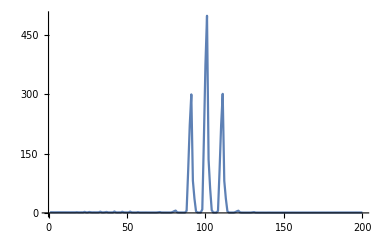

```mathematica
ListLinePlot[mapadc/@datsmp,PlotRange->All]
```

```mathematica
mapdb=260.77279439909387 Log[77.83900848865268 #]&
```

260.773 Log[77.839 #1]&

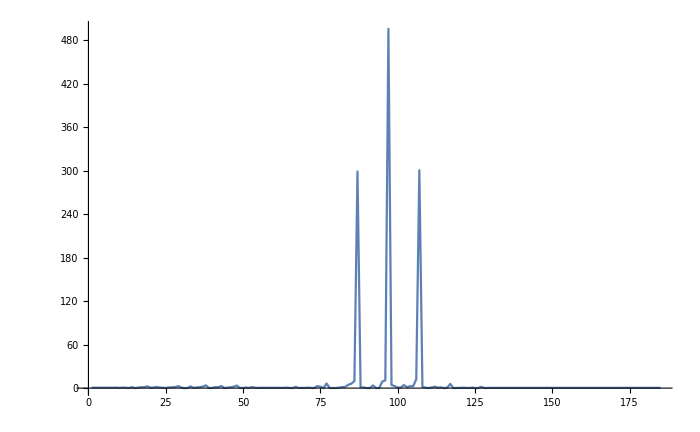

```mathematica
ListLinePlot[Abs@ListConvolve[deconvker,mapadc/@datsmp],PlotRange->All]
```

```mathematica
Sin[2π 100 t]Sin[2π 100 t]
```

Sin[200 π t]^2

```mathematica
mapdb=260.77279439909387 Log[77.83900848865268 #]&
```

260.773 Log[77.839 #1]&

```mathematica
mapadc=0.012847029007901344 ⅇ^(0.003834755854437685 #)&
```

0.012847 ⅇ^(0.00383476 #1)&

```mathematica
deconvker
```

{0.0148189,-0.0112552,-0.0139333,0.053656,-0.0694247,0.00448376,0.157711,-0.312902,0.221711,0.32478,-1.15388,1.44223,-0.167504,-0.1426,0.0349846,0.0106429}